```mathematica
elec to muon
A11= Cos[θ21]Cos[θ31]
A21= Sin[θ21] Cos[θ31]
A31= Sin[θ31] Exp[-I*σ]
A32= Sin[θ31]Exp[I*σ]
B11=-(Sin[θ21]Cos[θ32])-(Cos[θ21]Sin[θ32]Sin[θ31]Exp[I*σ])
B12= -(Sin[θ21]Cos[θ32])-(Cos[θ21]Sin[θ32]Sin[θ31]Exp[-I*σ])
B21=((Cos[θ21]Cos[θ32])-(Sin[θ21]Sin[θ32]Sin[θ31]Exp[I*σ]))
B22=((Cos[θ21]Cos[θ32])-(Sin[θ21]Sin[θ32]Sin[θ31]Exp[-I*σ]))
B31=Sin[θ32]Cos[θ31]
B32=B31
l/e=bass
δm31=δm32-δm21
```

elec muon to

Cos[θ21] Cos[θ31]

Cos[θ31] Sin[θ21]

ⅇ^(-ⅈ σ) Sin[θ31]

ⅇ^(ⅈ σ) Sin[θ31]

-Cos[θ32] Sin[θ21]-ⅇ^(ⅈ σ) Cos[θ21] Sin[θ31] Sin[θ32]

-Cos[θ32] Sin[θ21]-ⅇ^(-ⅈ σ) Cos[θ21] Sin[θ31] Sin[θ32]

Cos[θ21] Cos[θ32]-ⅇ^(ⅈ σ) Sin[θ21] Sin[θ31] Sin[θ32]

Cos[θ21] Cos[θ32]-ⅇ^(-ⅈ σ) Sin[θ21] Sin[θ31] Sin[θ32]

Cos[θ31] Sin[θ32]

Cos[θ31] Sin[θ32]

Set::write: Tag Times in l/e is Protected.

bass

-δm21+δm32

DifferenceDelta::novar: ∆ m31 cannot be interpreted. The operator "\[DifferenceDelta]" requires a subscript with a variable specification.

```mathematica
P1=σ
P2=4Re[((A21*B21*A11*B12)(Sin[(((δm21)^2)*bass*1.27)])^2)+((A32*B31*A21*B22)(Sin[(((δm32)^2)*bass*1.27 )])^2)+((A32*B31*A11*B12)(Sin[(((δm31)^2)*bass*1.27 )])^2)]
P3=2Im[(((A21*B21*A11*B12)Sin[(((δm21)^2)*bass*1.27)])+((A32*B31*A21*B22)Sin[(((δm32)^2)*bass*1.27)])+((A32*B31*A11*B12)Sin[(((δm31)^2)*bass*1.27)]))]
```

σ

4 Re[ⅇ^(ⅈ σ) Cos[θ21] Cos[θ31]^2 Sin[1.27 bass (-δm21+δm32)^2]^2 Sin[θ31] Sin[θ32] (-Cos[θ32] Sin[θ21]-ⅇ^(-ⅈ σ) Cos[θ21] Sin[θ31] Sin[θ32])+ⅇ^(ⅈ σ) Cos[θ31]^2 Sin[1.27 bass δm32^2]^2 Sin[θ21] Sin[θ31] Sin[θ32] (Cos[θ21] Cos[θ32]-ⅇ^(-ⅈ σ) Sin[θ21] Sin[θ31] Sin[θ32])+Cos[θ21] Cos[θ31]^2 Sin[1.27 bass δm21^2]^2 Sin[θ21] (-Cos[θ32] Sin[θ21]-ⅇ^(-ⅈ σ) Cos[θ21] Sin[θ31] Sin[θ32]) (Cos[θ21] Cos[θ32]-ⅇ^(ⅈ σ) Sin[θ21] Sin[θ31] Sin[θ32])]

2 Im[ⅇ^(ⅈ σ) Cos[θ21] Cos[θ31]^2 Sin[1.27 bass (-δm21+δm32)^2] Sin[θ31] Sin[θ32] (-Cos[θ32] Sin[θ21]-ⅇ^(-ⅈ σ) Cos[θ21] Sin[θ31] Sin[θ32])+ⅇ^(ⅈ σ) Cos[θ31]^2 Sin[1.27 bass δm32^2] Sin[θ21] Sin[θ31] Sin[θ32] (Cos[θ21] Cos[θ32]-ⅇ^(-ⅈ σ) Sin[θ21] Sin[θ31] Sin[θ32])+Cos[θ21] Cos[θ31]^2 Sin[1.27 bass δm21^2] Sin[θ21] (-Cos[θ32] Sin[θ21]-ⅇ^(-ⅈ σ) Cos[θ21] Sin[θ31] Sin[θ32]) (Cos[θ21] Cos[θ32]-ⅇ^(ⅈ σ) Sin[θ21] Sin[θ31] Sin[θ32])]

```mathematica
P1-P2-P3
```

-2 Im[-0.139207 Sin[0.0001016 bass]-0.0317636 Sin[0.00193306 bass]+0.0258624 Sin[0.002921 bass]]-4 Re[-0.139207 Sin[0.0001016 bass]^2-0.0317636 Sin[0.00193306 bass]^2+0.0258624 Sin[0.002921 bass]^2]

```mathematica
f[bass_]=(P1-P2-P3)
```

-2 Im[-0.139207 Sin[0.0001016 bass]-0.0317636 Sin[0.00193306 bass]+0.0258624 Sin[0.002921 bass]]-4 Re[-0.139207 Sin[0.0001016 bass]^2-0.0317636 Sin[0.00193306 bass]^2+0.0258624 Sin[0.002921 bass]^2]

```mathematica
σ=0
θ21=0.48240901
θ31=0.1586504
θ32=0.5148721
δm21=Sqrt[8*^-5]
δm32=Sqrt[2.3*^-3]
check
```

0

0.482409

0.15865

0.514872

1/(50 √5)

0.0479583

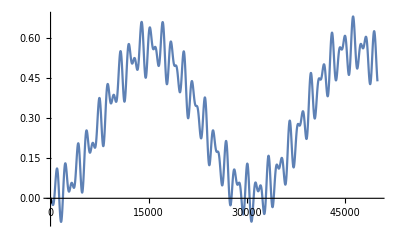

```mathematica
Plot[f[bass],{bass,0,50*^3}]
```

```mathematica
.
```

```mathematica
f[test]=1-(((Sin[2*y])^2)*((Sin[((δm31)^2)*(bass*1.27)])^2))
```

1-0.097346 Sin[0.00193306 bass]^2

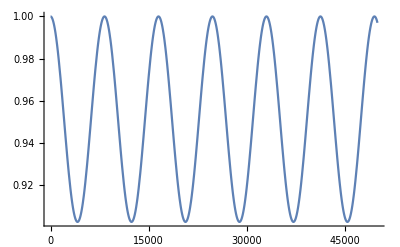

```mathematica
Plot[1-0.09734602275129449 Sin[0.0003805238941047278 bass]^2,{bass,0,50000}]
```

```mathematica
θ
```